```mathematica
Clear["Global`*"]
```

```mathematica
g=9.81;
l = 1;
poc=1;
time = {t, 0, 10};
init = {y[0] == poc, y'[0] == 0};
rovnice = y''[t] == - g/l*Sin[y[t]];
```

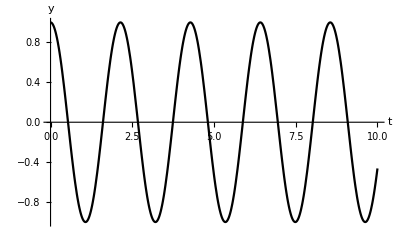

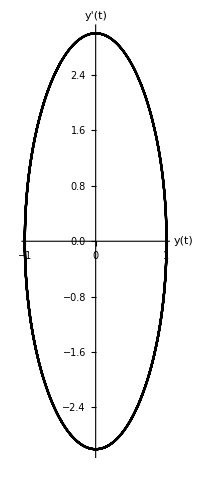

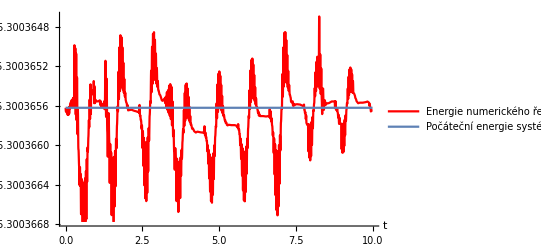

```mathematica
sol=NDSolve[{y''[t]  +g/l*Sin[y[t]]==0, y[0] == poc, y'[0] == 0}, y, time];
Plot[
Evaluate[y[t] /. sol], time,
AxesLabel->{
Style[ToExpression["t",TeXForm,HoldForm],Larger],
Style[ToExpression["y",TeXForm,HoldForm],Larger]
},
PlotStyle->Black
]
ParametricPlot[
Evaluate[{y[t], y'[t]}/. sol],Evaluate[time],
AxesLabel->{
Style[ToExpression["y(t)",TeXForm,HoldForm],Larger],
Style[ToExpression["y'(t)",TeXForm,HoldForm],Larger]
},
PlotStyle->Black
]
p1=Plot[Evaluate[1/2 *(y'[t])^2-g/l *Cos[y[t]]/. sol], time,PlotStyle->Red,PlotLegends->{"Energie numerického řešení v čase"},
AxesLabel->{
Style[ToExpression["t",TeXForm,HoldForm],Larger]
}] ;
p2 = Plot[-g/l *Cos[poc],time, PlotStyle->Thick,PlotLegends->{"Počáteční energie systému"},
AxesLabel->{
Style[ToExpression["t",TeXForm,HoldForm],Larger]
}];
Show[p1,p2,PlotRange->All]
```

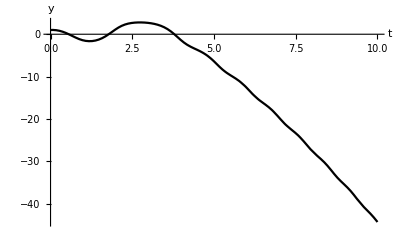

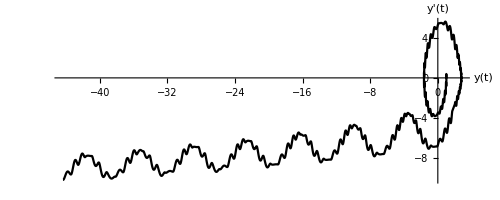

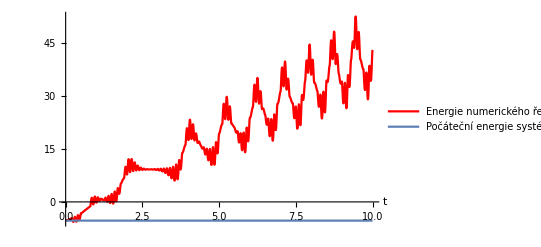

```mathematica
solEU=NDSolve[{y''[t]  +g/l*Sin[y[t]]==0, y[0] == poc, y'[0] == 0}, y, time,Method->"ExplicitEuler",StartingStepSize->0.1,MaxStepSize->0.1,MaxSteps->100];
Plot[
Evaluate[y[t] /. solEU], time,
AxesLabel->{
Style[ToExpression["t",TeXForm,HoldForm],Larger],
Style[ToExpression["y",TeXForm,HoldForm],Larger]
},
PlotStyle->Black
]
ParametricPlot[
Evaluate[{y[t], y'[t]}/. solEU],Evaluate[time],
AxesLabel->{
Style[ToExpression["y(t)",TeXForm,HoldForm],Larger],
Style[ToExpression["y'(t)",TeXForm,HoldForm],Larger]
},
PlotStyle->Black
]
p1=Plot[Evaluate[1/2 *(y'[t])^2-g/l *Cos[y[t]]/. solEU], time,PlotStyle->Red,PlotLegends->{"Energie numerického řešení v čase"},
AxesLabel->{
Style[ToExpression["t",TeXForm,HoldForm],Larger]
}] ;
p2 = Plot[-g/l *Cos[poc],time, PlotStyle->Thick,PlotLegends->{"Počáteční energie systému"},
AxesLabel->{
Style[ToExpression["t",TeXForm,HoldForm],Larger]
}];
Show[p1,p2,PlotRange->All]
```

```mathematica
H = p[t]^2/2 -g/l *Cos[q[t]];
eqs = {p'[t] == -D[H, q[t]], q'[t] == D[H, p[t]]};
ics = {p[0] == 0,q[0] == poc};
vars = {q[t], p[t]};
```

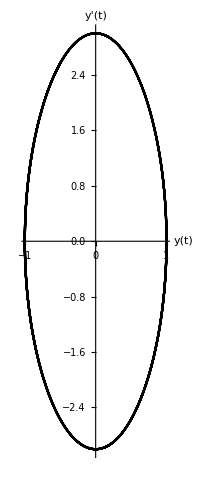

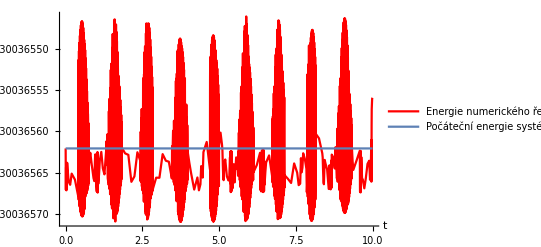

```mathematica
rese=NDSolve[{eqs,ics},vars,time,Method->{"SymplecticPartitionedRungeKutta","DifferenceOrder"->4,"PositionVariables"->{q[t]}}];
ParametricPlot[
Evaluate[vars/. rese],Evaluate[time],
AxesLabel->{
Style[ToExpression["y(t)",TeXForm,HoldForm],Larger],
Style[ToExpression["y'(t)",TeXForm,HoldForm],Larger]
},
PlotStyle->Black
]
p1=Plot[Evaluate[p[t]^2/2 -g/l *Cos[q[t]]/.rese], time,PlotStyle->Red,PlotLegends->{"Energie numerického řešení v čase"},
AxesLabel->{
Style[ToExpression["t",TeXForm,HoldForm],Larger]
}] ;
p2 = Plot[-g/l *Cos[poc],time, PlotStyle->Thick,PlotLegends->{"Počáteční energie systému"},
AxesLabel->{
Style[ToExpression["t",TeXForm,HoldForm],Larger]
}];
Show[p1,p2,PlotRange->All]
```

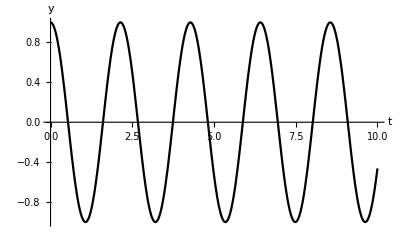

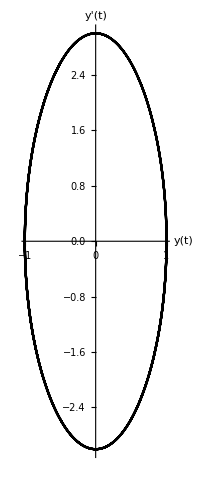

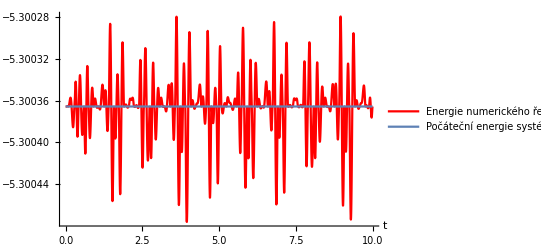

```mathematica
solP=NDSolve[{y''[t] + g/l *Sin[y[t]] == 0, y[0] == poc, y'[0] == 0}, y, time,Method->{"Projection",Method->"ExplicitRungeKutta","Invariants"->-g/l *Cos[poc]}];
Plot[
Evaluate[y[t] /. solP], time,
AxesLabel->{
Style[ToExpression["t",TeXForm,HoldForm],Larger],
Style[ToExpression["y",TeXForm,HoldForm],Larger]
},
PlotStyle->Black
]
ParametricPlot[
Evaluate[{y[t], y'[t]}/. solP],Evaluate[time],
AxesLabel->{
Style[ToExpression["y(t)",TeXForm,HoldForm],Larger],
Style[ToExpression["y'(t)",TeXForm,HoldForm],Larger]
},
PlotStyle->Black
]
p1=Plot[Evaluate[1/2 *(y'[t])^2-g/l *Cos[y[t]]/. solP], time,PlotStyle->Red,PlotLegends->{"Energie numerického řešení v čase"},
AxesLabel->{
Style[ToExpression["t",TeXForm,HoldForm],Larger]
}] ;
p2 = Plot[-g/l *Cos[poc],time, PlotStyle->Thick,PlotLegends->{"Počáteční energie systému"},
AxesLabel->{
Style[ToExpression["t",TeXForm,HoldForm],Larger]
}];
Show[p1,p2,PlotRange->All]
```

```mathematica
tabulka0=Table[t, {t,0,10, 1 }];
tabulkaA=Table[Evaluate[1/2 *(y'[t])^2-g/l *Cos[y[t]]/. sol], {t,0,10, 1 }];
tabulkaB=Table[Evaluate[p[t]^2/2 -g/l *Cos[q[t]]/.rese], {t,0,10, 1 }] ;
tabulkaC=Table[Evaluate[1/2 *(y'[t])^2-g/l *Cos[y[t]]/. solP], {t,0,10, 1 }];
NumberForm[Grid[{{"Čas","NDSolve","SymplecticRungeKutta","Projection"},{TableForm[tabulka0],TableForm[tabulkaA],TableForm[tabulkaB],TableForm[tabulkaC]}},Frame->All],10]
```

Čas | NDSolve | SymplecticRungeKutta | Projection
0
1
2
3
4
5
6
7
8
9
10 | -5.300365621
-5.300365503
-5.300365607
-5.300365352
-5.300365507
-5.300365437
-5.300365525
-5.300366032
-5.300366084
-5.300365929
-5.300365649 | -5.300365621
-5.300365669
-5.300365639
-5.300365644
-5.300365646
-5.300365575
-5.300365688
-5.300365495
-5.300365652
-5.300365615
-5.300365559 | -5.300365621
-5.300364618
-5.300365847
-5.300351305
-5.300348124
-5.300357624
-5.300343897
-5.300362859
-5.300399387
-5.300377653
-5.300365623

----------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------PERIODA

```mathematica
GetPeriodN[initpos_]:=(
tend := 0;
NDSolve[{y''[t] == - g/l*Sin[y[t]], y[0]==initpos, y'[0] == 0, WhenEvent[y[t]==0, {tend = t, "StopIntegration"}]}, y, {t,0, 2*Pi*Sqrt[l/g] }];
4*tend
)
GetPeriodEU[initpos_]:=(
tend := 0;
NDSolve[{y''[t] == - g/l*Sin[y[t]], y[0]==initpos, y'[0] == 0, WhenEvent[y[t]==0, {tend = t, "StopIntegration"}]}, y, {t,0, 2*Pi*Sqrt[l/g] },Method->"ExplicitEuler",StartingStepSize->0.1,MaxStepSize->0.1,MaxSteps->100];
4*tend
)
GetPeriodS[initpos_]:=(
tend := 0;
NDSolve[{eqs,{p[0] == 0,q[0] == initpos},WhenEvent[q[t]==0, {tend = t, "StopIntegration"}]},vars,time,Method->{"SymplecticPartitionedRungeKutta","DifferenceOrder"->4,"PositionVariables"->{q[t]}}];
4*tend
)
```

```mathematica
PeriodaAprox[θ_] := 2*Pi*Sqrt[l/g]*(1+θ^2/16+11*θ^4/3072)
PeriodaAproxLin[θ_] := 2*Pi*Sqrt[l/g]
```

```mathematica
ElipInt[θ_]:=Integrate[4*Sqrt[l/g]*1/Sqrt[1-Sin[θ/2]^2*Sin[y]^2],{y,0,Pi/2}]
```

```mathematica
tab1=Table[ initpos, {initpos,1/1000, Pi/2,0.3 }];
tab2=Table[ GetPeriodN[initpos], {initpos,1/1000, Pi/2,0.3 }];
tab3=Table[ GetPeriodS[initpos], {initpos,1/1000, Pi/2,0.3 }];
tab4=Table[ GetPeriodEU[initpos], {initpos,1/1000, Pi/2,0.3 }];
tab5=Table[ PeriodaAprox[initpos], {initpos,1/1000, Pi/2, 0.3 }];
tab6=Table[ Re[ElipInt[initpos]], {initpos,1/1000, Pi/2, 0.3 }];
tab7=Table[ PeriodaAproxLin[initpos], {initpos,1/1000, Pi/2, 0.3 }];
Grid[{{"Počáteční výchylka","NDSolve","Symplectic RungeKutta","Eulerova metoda", "Aproximace periody","Přímou integrací","Lin. rovnice"},{TableForm[tab1],TableForm[tab2],TableForm[tab3],TableForm[tab4],TableForm[tab5],TableForm[tab6],TableForm[tab7]}},Frame->All]
```

Počáteční výchylka | NDSolve | Symplectic RungeKutta | Eulerova metoda | Aproximace periody | Přímou integrací | Lin. rovnice
0.001
0.301
0.601
0.901
1.201
1.501 | 2.00605
2.01749
2.05231
2.11285
2.20344
2.33149 | 2.00607
2.01749
2.05231
2.11285
2.20344
2.33149 | 2.06809
2.08132
2.12202
2.19407
2.30382
2.45399 | 2.00607
2.01749
2.05229
2.11258
2.20186
2.32501 | 2.00607
2.01749
2.05231
2.11285
2.20344
2.33149 | 2.00607
2.00607
2.00607
2.00607
2.00607
2.00607

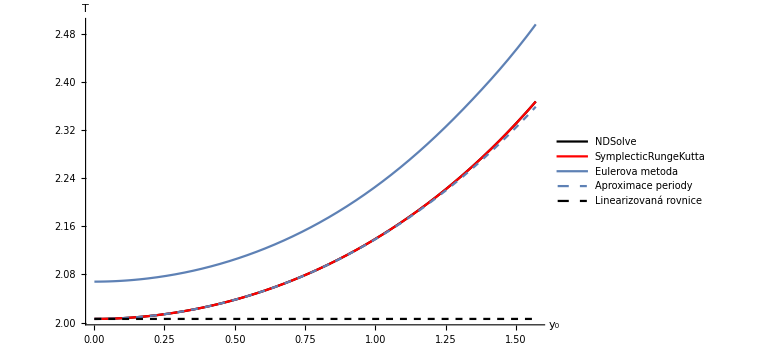

```mathematica
pp1=Plot[ GetPeriodN[initpos], {initpos,1/1000, Pi/2},
AxesLabel->{
Style[ToExpression["y_{0}",TeXForm,HoldForm],Larger],
Style[ToExpression["T",TeXForm,HoldForm],Larger]
},
PlotStyle->Black, PlotRange->{{0,1.6},{1.9,2.6}},PlotLegends->{"NDSolve"}
] ;
pp2=Plot[ GetPeriodS[initpos], {initpos,1/1000, Pi/2},
AxesLabel->{
Style[ToExpression["y_{0}",TeXForm,HoldForm],Larger],
Style[ToExpression["T",TeXForm,HoldForm],Larger]
},
PlotStyle->Red, PlotRange->{{0,1.6},{1.9,2.6}},PlotLegends->{"SymplecticRungeKutta"}
] ;
pp3=Plot[ GetPeriodEU[initpos], {initpos,1/1000, Pi/2},
AxesLabel->{
Style[ToExpression["y_{0}",TeXForm,HoldForm],Larger],
Style[ToExpression["T",TeXForm,HoldForm],Larger]
},
PlotStyle->Thick, PlotRange->{{0,1.6},{1.9,2.6}},PlotLegends->{"Eulerova metoda"}
] ;
pp4=Plot[ PeriodaAprox[initpos], {initpos,1/1000, Pi/2},
AxesLabel->{
Style[ToExpression["y_{0}",TeXForm,HoldForm],Larger],
Style[ToExpression["T",TeXForm,HoldForm],Larger]
},
PlotStyle->Dashed, PlotRange->{{0,1.6},{1.9,2.6}},PlotLegends->{"Aproximace periody"}
] ;
pp5=Plot[ PeriodaAproxLin[initpos], {initpos,1/1000, Pi/2},
AxesLabel->{
Style[ToExpression["y_{0}",TeXForm,HoldForm],Larger],
Style[ToExpression["T",TeXForm,HoldForm],Larger]
},
PlotStyle->{Dashed,Black}, PlotRange->{{0,1.6},{1.9,2.6}},PlotLegends->{"Linearizovaná rovnice"}
] ;
Show[pp1,pp2,pp3,pp4,pp5,PlotRange->All, ImageSize->Large]
```